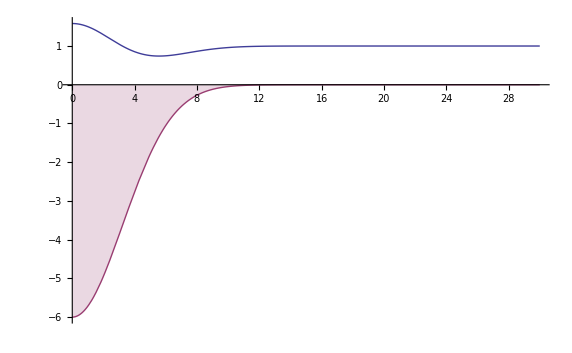

```mathematica
σ=1/0.22;
t=1;
τ=1;
A=6;
z[x_,t_]:=(1-ⅇ^(-(x/σ)^2))(1-ⅇ^(-t/τ));
z[x_]:=A(1-ⅇ^(-(x/σ)^2));
r=D[D[z[x], x], x];
Plot[{r+1,z[x]-A},{x,0,30},Filling->{2->Axis},PlotRange->Full]
```

```mathematica
Clear[t,τ,z,r,σ]
τ=1; σ=1;Subscript[ϱ, s]=1;Subscript[ϱ, r]=2;Κ=1;
z[x_,t_]=(1-ⅇ^(-(x/σ)^2))(ⅇ^(-t/τ)-1);
Plot3D[z[x,t],{x,0,3},{t,0,4}];
```

```mathematica
eqn={(Subscript[ϱ, s]-Subscript[ϱ, r])h'[x,t]==-Subscript[ϱ, r]z'[x,t]+Subscript[ϱ, s] Κ D[(D[(z[x,t]), x]), x],z[x,0]==0,z[Inf,t]==0,h'[x,t]==0}
DSolve[eqn,h[x,t],x]
```

{-h'[x,t]==-4 ⅇ^(-x^2) x+z^(2,0)[x,t],z[x,0]==0,z[Inf,t]==0,h'[x,t]==0}

DSolve::deqx: Supplied equations are not differential equations of the given functions.

DSolve[{-h'[x,t]==-4 ⅇ^(-x^2) x+z^(2,0)[x,t],z[x,0]==0,z[Inf,t]==0,h'[x,t]==0},h[x,t],x]

```mathematica
Clear[t,τ,z,r,σ,f,h,y]
τ=1; σ=1;Subscript[ϱ, s]=1;Subscript[ϱ, r]=2;Κ=1;
z[x_]=(1-ⅇ^(-(x/σ)^2))(ⅇ^(-t/τ)-1);
```

{0.054+(0.1 (1.1616 ⅇ^(-0.0484 Rr^2) Rr-0.0562214 ⅇ^(-0.0484 Rr^2) Rr^3))/Rr}

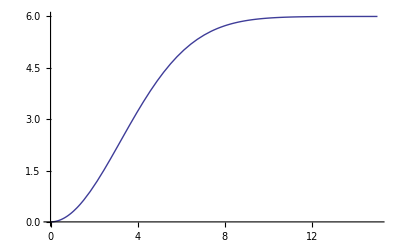
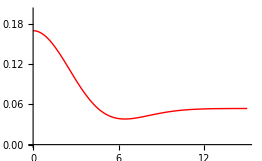

```mathematica
Needs["VectorAnalysis`"]
Clear[z,σ,F,K,h,y,Q,A]
z[Rr_]=A(1-ⅇ^(-(Rr/σ)^2));
σ=1/0.22;Subscript[ϱ, s]=1000;Subscript[ϱ, r]=2700;K=0.0001;F=20*10^(-6);A=6;
sol = DSolve[Q[Rr]==K*Subscript[ϱ, s]*Laplacian[z[Rr], Cylindrical]+F*Subscript[ϱ, r],Q,Rr];
Evaluate[Q[Rr]/.sol]
{Plot[z[x], {x,0,15},PlotStyle->Thick],
Plot[{Evaluate[Q[x]/.sol]}, {x,0,15},PlotStyle->{Red, Thick},PlotRange-> {0,0.2}]}
```